```mathematica
SetDirectory ["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/ZrC_analysis/MD-trajectory"];
fileMD={"def_traj_cart_periodic-Frenkel_500_222kp-6hr-9.700"};
dataMD= Table[ReadList[fileMD[[i]],Table[Number,{i,1,96}]],{i,1,Length[fileMD]}];
```

```mathematica
ListPointPlot3D@dataMD[[1]]
```

-Graphics3D-

```mathematica
dataMD[[1]]//Length
```

1024

```mathematica
ListPointPlot3D[Transpose[Table[Partition[dataMD[[1]][[i]],3],{i,1,1024}]][[1]],ImageSize->Large,PlotRange->{Automatic,Automatic,{3,7}},PlotStyle->PointSize[0.01]]
```

-Graphics3D-

```mathematica
Point[a___]:>{Thickness[0.004],Line[a]}
```

Point[a___]:>{Thickness[0.004],Line[a]}

```mathematica
colours=Table[Blend[{Blue,Red},i/1000],{i,1,1000}];
```

```mathematica
ListPointPlot3D[Transpose[Table[Partition[dataMD[[1]][[i]],3],{i,1,1000}]][[1;;32]],ImageSize->Large,PlotRange->{Automatic,Automatic,{1,6.2}},PlotStyle->colours,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Transpose[Table[Partition[dataMD[[1]][[i]],3],{i,1,100}]][[1;;32]],ImageSize->Large,PlotRange->{Automatic,Automatic,{1,6.2}},PlotStyle->colours,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Transpose[Table[Partition[dataMD[[1]][[i]],3],{i,101,200}]][[1;;32]],ImageSize->Large,PlotRange->{Automatic,Automatic,{1,6.2}},PlotStyle->colours,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Transpose[Table[Partition[dataMD[[1]][[i]],3],{i,1,100}]][[1;;32]],ImageSize->Large,PlotRange->{Automatic,Automatic,{1,6.2}},PlotStyle->colours,BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Transpose@Table[Partition[dataMD[[1]][[i]],3][[1;;2]],{i,1,50}],ImageSize->Large,PlotRange->{Automatic,Automatic,{-1,9}},PlotStyle->Joined]
```

-Graphics3D-

```mathematica
Transpose@Table[Partition[dataMD[[1]][[i]],3],{i,1,1024}]
```

{{{0.0878,2.2001,4.5973},{0.1348,2.171,4.5415},{0.1818,2.1261,4.493},{0.2245,2.0902,4.468},{0.2392,2.0868,4.4773},{0.2344,2.1134,4.4927},{0.2171,2.1565,4.5089},1011,{1.7068,5.0595,4.4292},{1.7405,5.0856,4.3775},{1.7428,5.1037,4.3408},{1.7568,5.1231,4.3419},{1.809,5.1441,4.3585},{1.8774,5.1525,4.416}},30,{1}}
 |  |  |  |

```mathematica
plotData=Transpose@Table[Table[Drop[Partition[dataMD[[1]][[j]],3][[i]],-1],{i,1,32}],{j,1,1024}];
```

```mathematica
plotData2=Transpose@Table[Table[Partition[dataMD[[1]][[j]],3][[i]],{i,1,32}],{j,1,1024}];
```

```mathematica
colours={PlotStyle->Table[Blend[{Blue,Red},i/1000],{i,1,1000}]};
```

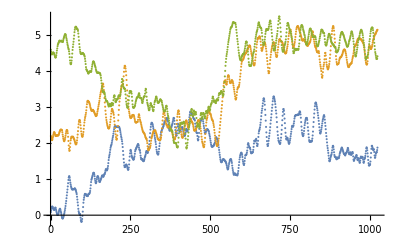

```mathematica
ListPlot@Transpose@plotData2[[1]]
```

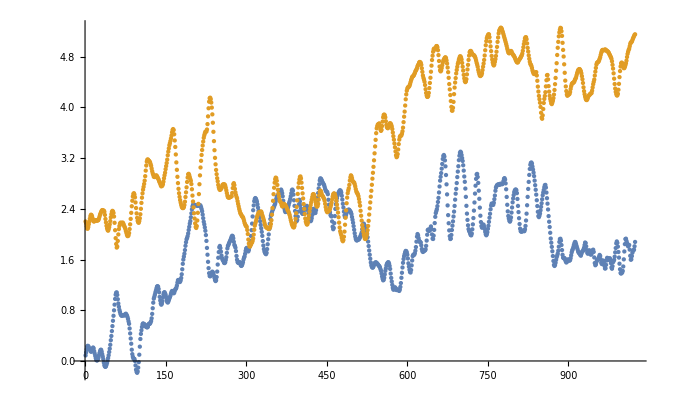

```mathematica
ListPlot@Transpose@plotData[[1]]
```

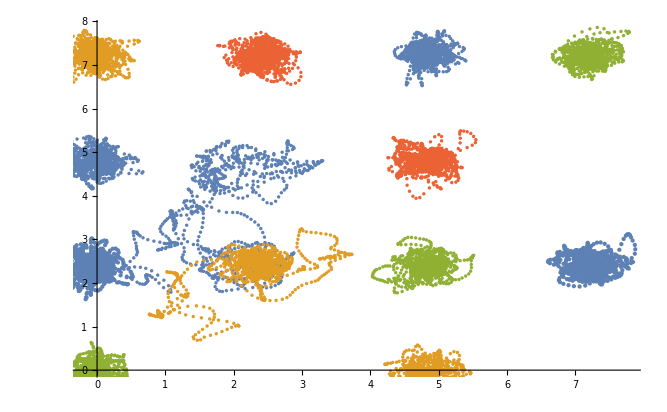

```mathematica
Show[{ListPlot@plotData[[1;;4]],ListPlot@plotData[[5;;5]],ListPlot@plotData[[10;;12]],ListPlot@plotData[[16;;16]],ListPlot@plotData[[18;;21]],ListPlot@plotData[[23;;22]]}]
```

```mathematica
ListPlot@Correlation[{Transpose[plotData2[[1]]][[1]],Transpose[plotData2[[1]]][[2]]}]
```

-Graphics-

```mathematica
Correlation@{Transpose[plotData2[[1]]][[1]][[1;;10]],Transpose[plotData2[[1]]][[2]][[1;;10]]}
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
data[[1]][[1]][[1]]
```

0.0878

```mathematica
Transpose[plotData2[[1]]][[1]][[1;;1024]]-Transpose[plotData2[[1]]][[1]][[1]];
```

```mathematica
Transpose[plotData2[[3]]][[1]]//Length
```

1024

{-0.222287,-0.745919,-0.0131801,0.0808203,-0.23131,0.0849623,0.0178703,0.0236216,0.117934,-0.0610508,0.150361,0.0572753,-0.122534,0.160475,-0.244741,-0.0246442,0.240617,0.0100576,0.0101045,-0.030841,-0.0784868,0.0777067,0.0396927,0.0179866,0.706794,-0.0717456,-0.0620057,0.0361294,-0.107877,-0.0930014,-0.03152,-0.245879}

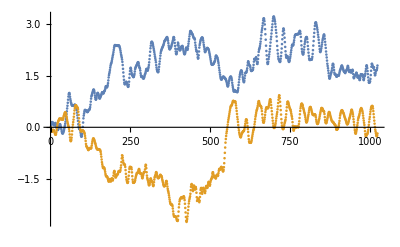
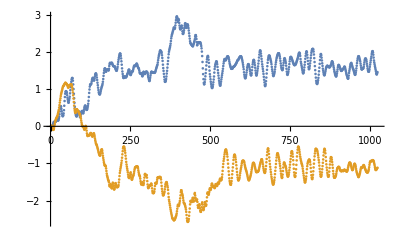
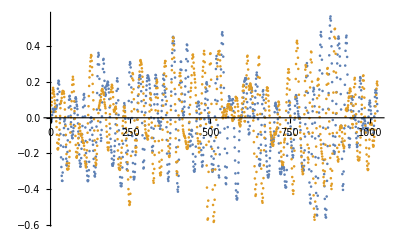
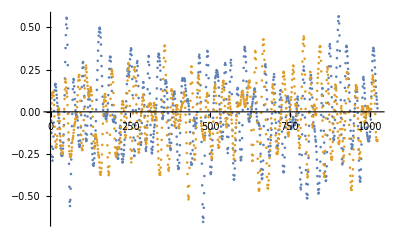
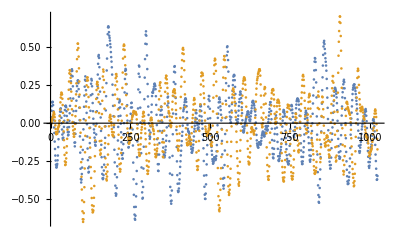
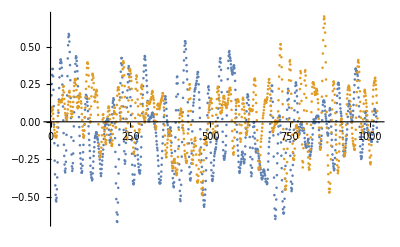
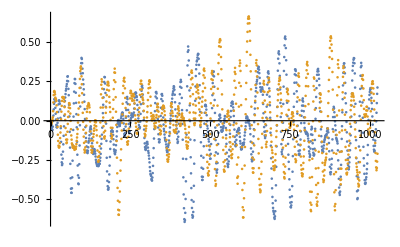
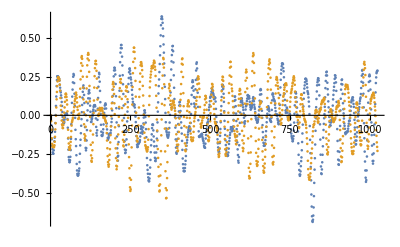

```mathematica
Autocorrelation - correlation of displacements in x with displacements in x for every atom;
data=Table[{Transpose[plotData2[[i]]][[1]][[1;;1024]]-Transpose[plotData2[[i]]][[1]][[1]],Transpose[plotData2[[i]]][[3]][[1;;1024]]-Transpose[plotData2[[i]]][[3]][[1]]},{i,1,32}];

Table[Correlation[data[[i]][[1]]-data[[i]][[1]][[1]],data[[i]][[2]]-data[[i]][[2]][[1]]],{i,1,32}]
Table[ListPlot[data[[i]]],{i,1,32}]
```

```mathematica
Defect-correlation - correlation of defect displacements in x with other atom displacements in x
```

{-0.222287,-0.709111,-0.0562855,0.0807085,0.0470137,-0.15309,-0.105374,-0.0950408,0.131629,-0.108702,-0.00973139,0.108405,-0.0752347,0.106396,0.0306203,0.109174,-0.144132,-0.00258618,-0.111829,0.021083,-0.062314,0.0266384,-0.0775482,0.00534982,0.406286,-0.0484692,0.0534681,-0.0288917,0.00947043,-0.0559941,-0.066808,-0.00816991}

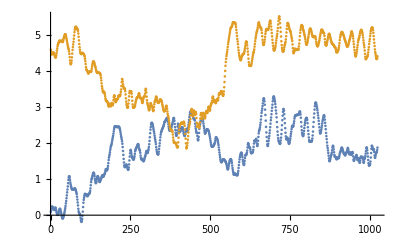
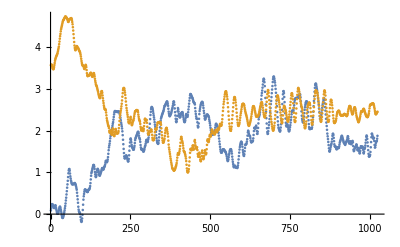
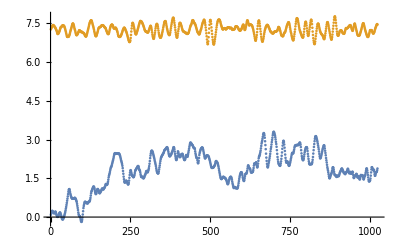
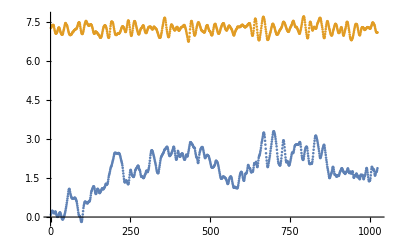
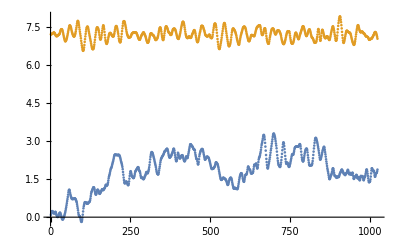
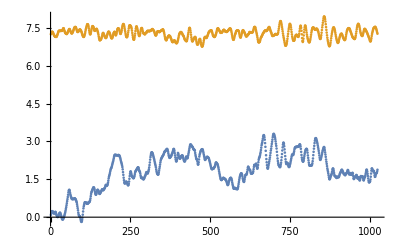
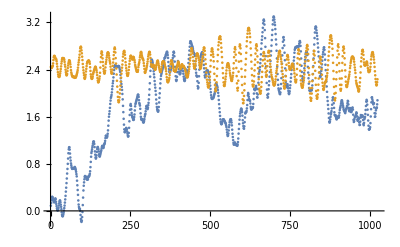
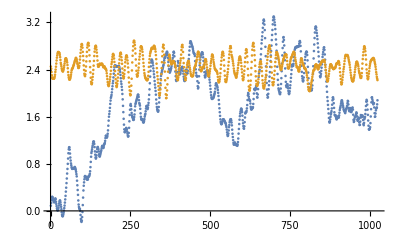

```mathematica
data=Table[{Transpose[plotData2[[1]]][[1]][[1;;1024]],Transpose[plotData2[[i]]][[3]][[1;;1024]]},{i,1,32}];
Table[Correlation[data[[1]][[1]]-data[[1]][[1]][[1]],data[[i]][[2]]],{i,1,32}]
Table[ListPlot[data[[i]]],{i,1,32}]
```

```mathematica
data[[1]][[1]]
```

{0.0878,0.1348,0.1818,0.2245,0.2392,0.2344,0.2171,0.1905,0.1789,0.1622,0.147,0.1479,0.17,0.1934,0.2125,0.1984,0.1547,0.1181,0.0808,0.0446,0.0159,0.0079,0.011,0.0272,0.0529,0.0906,0.1257,0.155,0.1754,0.1761,0.1471,0.1061,0.0696,0.0287,-0.0249,-0.0666,-0.0858,-0.0929,-0.083,-0.0579,-0.0291,0.0057,0.0469,0.0902,0.1413,0.1946,0.2554,0.3272,0.394,0.4714,0.5499,0.6339,0.7127,0.7986,0.8884,0.9789,1.0457,1.0766,1.0815,1.0415,0.9737,0.9067,0.8549,0.8062,0.7742,0.7417,0.7242,0.7134,0.7185,0.7199,0.7215,0.726,0.7172,0.7248,0.7362,0.7454,0.7326,0.7158,0.6954,0.6644,0.6248,0.586,0.5128,0.4348,0.3544,0.2722,0.1771,0.1077,0.0668,0.0416,0.0339,0.0321,-0.0009,-0.07,-0.1368,-0.1717,-0.1869,-0.1644,-0.1053,-0.0188,0.0988,0.2257,0.3467,0.4273,0.4844,0.5366,0.5773,0.5922,0.5856,0.5767,0.5766,0.567,0.545,0.5369,0.532,0.5305,0.5397,0.5723,0.5875,0.5847,0.5901,0.6083,0.6309,0.673,0.7428,0.8317,0.9195,0.9832,1.0129,1.0456,1.0811,1.1108,1.1448,1.1731,1.1798,1.1718,1.1368,1.0837,1.0107,0.9546,0.9077,0.8876,0.9046,0.9425,1.0014,1.0494,1.077,1.0853,1.0651,1.044,1.009,0.9615,0.9325,0.921,0.9362,0.9604,0.9854,1.008,1.0296,1.0624,1.0898,1.1042,1.1005,1.0829,1.0674,1.0765,1.1053,1.1306,1.1371,1.1552,1.1892,1.2367,1.2729,1.2782,1.2594,1.2443,1.2511,1.2726,1.3095,1.3671,1.4465,1.5326,1.5991,1.6463,1.6924,1.7494,1.8165,1.8729,1.9194,1.9406,1.9691,2.0122,2.066,2.1158,2.1661,2.2069,2.2666,2.3293,2.3906,2.4367,2.4617,2.4724,2.4627,2.4574,2.4588,2.4599,2.4571,2.4546,2.4486,2.4506,2.4543,2.4571,2.4602,2.4571,2.4498,2.4248,2.3958,2.3608,2.3089,2.2523,2.197,2.155,2.1071,2.0539,1.9855,1.8938,1.7833,1.6766,1.5638,1.4641,1.3843,1.3412,1.335,1.3515,1.3772,1.3951,1.4089,1.3977,1.3778,1.3444,1.3113,1.2779,1.2604,1.2723,1.3236,1.4101,1.5211,1.6281,1.7179,1.792,1.8145,1.7809,1.7254,1.6633,1.6227,1.598,1.5871,1.5671,1.5465,1.5444,1.5577,1.5944,1.6368,1.7055,1.7752,1.8142,1.8318,1.8545,1.8753,1.8939,1.9142,1.9373,1.962,1.9755,1.9678,1.9342,1.8798,1.8317,1.814,1.7882,1.7331,1.6563,1.5977,1.5601,1.5485,1.5493,1.5551,1.5587,1.5304,1.5087,1.4994,1.5073,1.5269,1.5579,1.6004,1.63,1.6488,1.6909,1.7374,1.7725,1.7834,1.7693,1.7405,1.7281,1.7524,1.7945,1.8345,1.8932,1.9705,2.0635,2.1668,2.2792,2.3781,2.4535,2.5199,2.5548,2.5697,2.559,2.5398,2.5118,2.4705,2.4196,2.3698,2.3197,2.2682,2.2051,2.1452,2.0927,2.0368,1.9733,1.8912,1.8211,1.7648,1.7281,1.7075,1.6923,1.6844,1.7064,1.7642,1.841,1.9204,1.9965,2.0811,2.1646,2.2382,2.2916,2.3228,2.3461,2.3759,2.3954,2.4158,2.4367,2.4623,2.4814,2.5183,2.5569,2.5923,2.5995,2.6035,2.6239,2.6473,2.6584,2.6749,2.6951,2.7037,2.682,2.6456,2.5978,2.5274,2.4573,2.4086,2.3726,2.3491,2.353,2.371,2.3911,2.4079,2.426,2.4583,2.4938,2.5213,2.5561,2.5977,2.6448,2.6921,2.7038,2.6846,2.6247,2.5349,2.4465,2.3656,2.2865,2.2247,2.2057,2.2249,2.277,2.3553,2.4658,2.5434,2.5154,2.4594,2.405,2.3619,2.3324,2.3203,2.3237,2.3414,2.3806,2.4089,2.4253,2.4312,2.4414,2.4462,2.4189,2.3744,2.3292,2.2791,2.2381,2.2134,2.2051,2.2186,2.2522,2.3017,2.3609,2.3991,2.3882,2.3521,2.3335,2.3368,2.3778,2.4425,2.5104,2.5791,2.6491,2.7224,2.7866,2.8474,2.8794,2.8761,2.8627,2.843,2.8228,2.8048,2.7911,2.7761,2.7482,2.7153,2.689,2.6762,2.6708,2.6622,2.6303,2.5432,2.4649,2.4034,2.3454,2.3004,2.2877,2.2793,2.2022,2.1181,2.0785,2.0993,2.1743,2.2859,2.3986,2.4713,2.521,2.5671,2.6092,2.6366,2.6555,2.6702,2.6881,2.6922,2.682,2.6567,2.6068,2.5465,2.4792,2.4204,2.3553,2.2971,2.2664,2.2803,2.3078,2.3364,2.3578,2.3784,2.3842,2.3865,2.3835,2.3685,2.3582,2.3431,2.3176,2.2715,2.2275,2.1806,2.1271,2.0699,2.0145,1.965,1.9274,1.9072,1.9004,1.9069,1.9139,1.9163,1.9193,1.9351,1.9527,1.9758,1.9949,2.0235,2.0772,2.1308,2.162,2.1655,2.1449,2.1275,2.1153,2.0931,2.0534,2.0051,1.9518,1.8834,1.8125,1.7423,1.6759,1.613,1.5536,1.5099,1.4849,1.4719,1.475,1.4903,1.5147,1.5376,1.5481,1.556,1.5536,1.5448,1.5351,1.5249,1.5143,1.5003,1.494,1.4764,1.4491,1.4238,1.3808,1.3341,1.2976,1.2718,1.2806,1.3131,1.366,1.4215,1.4592,1.5051,1.5299,1.5449,1.5562,1.5566,1.535,1.5001,1.4522,1.3786,1.3103,1.2541,1.2006,1.1544,1.1257,1.1279,1.1529,1.1625,1.1515,1.1298,1.1186,1.1232,1.1262,1.122,1.112,1.1051,1.1283,1.1686,1.2286,1.312,1.3913,1.4747,1.5486,1.608,1.6524,1.6851,1.7145,1.7362,1.7324,1.7114,1.6765,1.6169,1.5401,1.4878,1.4402,1.4044,1.3952,1.4349,1.5073,1.5855,1.6538,1.6746,1.6729,1.6774,1.7002,1.7404,1.7969,1.8823,1.9611,2.0021,1.9812,1.938,1.899,1.8794,1.8752,1.8686,1.824,1.7666,1.7337,1.7194,1.7276,1.7399,1.7416,1.7451,1.7613,1.8158,1.8987,1.9918,2.064,2.0734,2.0516,2.0529,2.0653,2.0944,2.1224,2.0786,1.9959,1.9308,1.9242,1.9769,2.0672,2.1751,2.2738,2.3332,2.3647,2.3943,2.4424,2.5081,2.5724,2.6579,2.7522,2.8444,2.905,2.9635,3.0331,3.1078,3.186,3.233,3.249,3.2251,3.1639,3.0699,2.9332,2.786,2.6276,2.4534,2.3004,2.1728,2.0596,1.9695,1.9234,1.9318,1.9876,2.0654,2.1339,2.2018,2.2789,2.356,2.4458,2.5444,2.6388,2.7139,2.8062,2.9005,2.9874,3.0718,3.1675,3.2374,3.2836,3.3012,3.287,3.2488,3.2009,3.1553,3.0871,3.0028,2.9099,2.826,2.7193,2.5887,2.4472,2.3244,2.2247,2.1397,2.079,2.0531,2.0349,2.0099,1.9869,1.9817,2.0105,2.0767,2.1546,2.2539,2.3719,2.4998,2.6402,2.7648,2.8724,2.9422,2.9505,2.9029,2.8087,2.6859,2.5581,2.4186,2.2913,2.1909,2.1281,2.1019,2.1208,2.1516,2.149,2.1188,2.0816,2.0373,1.9995,1.9828,1.9989,2.0308,2.0843,2.1325,2.195,2.2592,2.3219,2.3933,2.4514,2.4828,2.4768,2.4611,2.4647,2.496,2.5516,2.61,2.6849,2.7353,2.757,2.7726,2.7789,2.7841,2.7832,2.7789,2.7814,2.7945,2.7929,2.7905,2.7895,2.7903,2.8065,2.8395,2.8743,2.8839,2.8609,2.8013,2.7084,2.5874,2.4637,2.3601,2.2868,2.2472,2.2123,2.1975,2.2173,2.2643,2.3404,2.421,2.5022,2.564,2.6166,2.6615,2.6869,2.7009,2.7045,2.6928,2.647,2.5555,2.4457,2.3487,2.2521,2.16,2.0872,2.0484,2.0399,2.0408,2.0472,2.0549,2.0556,2.0481,2.049,2.0773,2.1301,2.2156,2.3239,2.4564,2.5883,2.7139,2.8248,2.9347,3.0287,3.0946,3.1235,3.1305,3.1123,3.0659,3.019,2.9714,2.9158,2.8452,2.7727,2.7003,2.6236,2.5353,2.4439,2.3529,2.286,2.2691,2.2921,2.3261,2.3763,2.4314,2.4876,2.5504,2.6134,2.6575,2.6972,2.7399,2.7717,2.7772,2.7354,2.6563,2.5673,2.4817,2.3895,2.2851,2.1963,2.1128,2.022,1.9313,1.8658,1.7999,1.7306,1.6549,1.5774,1.5162,1.4986,1.5147,1.5507,1.5965,1.6372,1.6639,1.6931,1.7392,1.8031,1.8779,1.9219,1.9279,1.8973,1.8286,1.749,1.6741,1.6307,1.6211,1.6222,1.6196,1.5933,1.5706,1.5531,1.5629,1.5836,1.6015,1.5962,1.5842,1.5835,1.5915,1.6218,1.6667,1.713,1.7443,1.7642,1.7917,1.8256,1.8532,1.8775,1.8733,1.8455,1.816,1.7858,1.7586,1.727,1.7077,1.7019,1.6913,1.6727,1.66,1.6877,1.7168,1.73,1.7361,1.7596,1.7864,1.8284,1.8686,1.8588,1.8082,1.749,1.7085,1.6917,1.7064,1.7392,1.7451,1.7078,1.6811,1.6783,1.6938,1.7213,1.7459,1.7554,1.7202,1.6331,1.5453,1.5099,1.5231,1.5594,1.5953,1.6028,1.5951,1.6079,1.6451,1.6726,1.6562,1.6061,1.5526,1.5292,1.5384,1.5653,1.5845,1.5631,1.5,1.4587,1.4619,1.5163,1.5843,1.6271,1.6215,1.5952,1.5952,1.6119,1.6209,1.5974,1.543,1.4753,1.455,1.4943,1.5577,1.5781,1.5958,1.6453,1.7132,1.7816,1.8547,1.8855,1.8632,1.804,1.7191,1.6304,1.5343,1.4466,1.3879,1.3781,1.3905,1.3954,1.4208,1.4903,1.6028,1.7272,1.8432,1.9229,1.929,1.8944,1.8625,1.829,1.8086,1.8233,1.8297,1.7563,1.6588,1.5973,1.603,1.6539,1.7068,1.7405,1.7428,1.7568,1.809,1.8774}

```mathematica
Correlation[N[{1,2,8},20],N[{2,3,4},20]]
Correlation[{0.0878,0.1348,0.1818,0.2245,0.2392,0.2344,0.2171,0.1905,0.1789,0.1622,0.147,0.1479,0.17,0.1934,0.2125,0.1984,0.1547,0.1181,0.0808,0.0446,0.0159,0.0079,0.011,0.0272,0.0529,0.0906,0.1257,0.155,0.1754,0.1761,0.1471,0.1061,0.0696,0.0287,-0.0249,-0.0666,-0.0858,-0.0929,-0.083,-0.0579},{7.2515,7.2583,7.2584,7.2646,7.2684,7.2676,7.2727,7.277,7.2791,7.2759,7.2591,7.2289,7.1932,7.1442,7.0893,7.0524,7.0223,7.0115,7.0153,7.0189,7.0235,7.0141,6.994,6.9679,6.9503,6.9388,6.9468,6.9763,7.0219,7.0801,7.1502,7.2169,7.2667,7.3039,7.3581,7.4205,7.4781,7.5254,7.5629,7.572}]
```

0.924473451641905006

-0.352128

```mathematica
Correlation[{1.5,3,5,10},{2,1.25,15,8}]
```

0.475976

```mathematica
Correlation[data[[1]],data[[2]]]
```

-0.352218